```mathematica
Solve[1/x+1/y==1/4&&x>0 && y>0 && x≥y,{x,y},Integers]
```

{{x→8,y→8},{x→12,y→6},{x→20,y→5}}

```mathematica
s[n_]:=Solve[1/x+1/y==1/n&&x>0 && y>0 && x≥y,{x,y},Integers];
```

```mathematica
nSolutions=Table[Length[s[n]],{n,4,1000}]
```

{3,2,5,2,4,3,5,2,8,2,5,5,5,2,8,2,8,5,5,2,11,3,5,4,8,2,14,2,6,5,5,5,13,2,5,5,11,2,14,2,8,8,5,2,14,3,8,5,8,2,11,5,11,5,5,2,23,2,5,8,7,5,14,2,8,5,14,2,18,2,5,8,8,5,14,2,14,5,5,2,23,5,5,5,11,2,23,5,8,5,5,5,17,2,8,8,13,2,14,2,11,14,5,2,18,2,14,5,14,2,14,5,8,8,5,5,32,3,5,5,8,4,23,2,8,5,14,2,23,5,5,11,11,2,14,2,23,5,5,5,23,5,5,8,8,2,23,2,11,8,14,5,23,2,5,5,17,5,14,2,8,14,5,2,32,3,14,8,8,2,14,8,14,5,5,2,38,2,14,5,11,5,14,5,8,11,14,2,20,2,5,14,13,2,23,2,18,5,5,5,23,5,5,8,14,5,41,2,8,5,5,5,25,5,5,5,23,5,14,2,17,13,5,2,23,2,14,14,11,2,23,5,8,5,14,2,41,2,8,6,8,8,14,5,11,5,11,2,38,5,5,14,9,2,14,5,23,8,5,2,32,5,14,5,8,2,32,2,14,14,5,8,23,2,5,8,32,2,14,2,8,14,14,5,28,3,14,5,8,2,23,5,11,11,5,5,38,5,5,5,14,5,23,2,23,5,14,2,32,2,5,23,8,2,14,5,20,5,14,5,23,8,5,5,11,5,41,2,8,8,5,5,41,2,8,5,23,5,23,4,11,14,5,2,23,2,23,11,17,2,14,5,8,14,5,2,53,3,5,8,23,5,14,2,14,8,14,5,23,2,14,11,11,5,32,2,23,5,5,2,23,14,5,8,8,2,41,5,18,5,5,5,38,2,5,14,23,2,14,5,8,14,14,5,32,2,14,5,8,5,23,5,17,5,14,2,68,2,5,8,11,8,14,5,8,14,14,2,32,2,14,14,8,5,14,2,32,13,14,2,23,5,5,5,20,2,38,5,8,5,5,14,32,2,5,11,23,2,41,2,14,14,5,2,38,5,14,5,11,5,14,8,23,8,5,2,50,5,5,14,13,5,17,2,11,5,23,2,23,5,14,23,14,5,14,2,18,5,5,2,53,5,14,8,8,2,41,5,10,11,5,5,23,5,14,5,32,2,23,2,8,23,5,5,41,3,14,8,23,5,14,5,11,5,5,8,53,2,5,5,17,5,41,2,8,8,23,5,32,5,5,14,8,2,23,5,41,14,5,2,23,5,5,14,11,2,41,2,23,5,14,8,33,2,8,5,23,5,14,5,11,23,5,2,38,5,14,5,14,2,32,14,8,5,14,2,53,2,14,8,8,8,14,2,17,14,14,5,38,2,5,14,32,2,14,2,23,11,5,5,41,5,5,14,8,5,68,2,11,5,5,5,23,8,14,8,23,2,14,2,23,14,14,2,32,5,23,14,8,2,14,5,14,8,14,2,68,2,5,14,11,14,23,5,8,5,14,5,50,2,5,18,13,2,14,5,32,5,14,2,38,5,11,5,14,5,41,2,8,23,5,5,32,5,5,5,38,2,32,5,20,14,5,5,23,2,14,8,11,5,41,14,8,5,5,2,68,5,8,5,8,8,23,2,32,7,14,5,23,2,5,23,17,5,23,2,23,14,14,2,32,5,5,8,23,5,32,2,14,5,14,5,53,2,5,14,32,2,14,5,8,23,5,5,26,2,41,5,8,2,23,8,11,14,5,5,68,5,14,11,23,5,14,2,8,5,14,5,53,5,5,14,8,2,41,5,28,8,5,5,23,14,14,5,11,2,41,2,23,5,14,5,41,5,5,23,23,2,14,2,11,23,14,2,38,2,14,5,20,8,14,5,23,11,5,2,95,3,5,5,8,8,23,8,14,5,23,5,23,2,14,23,11,2,41,2,23,14,5,2,39,5,5,8,23,5,41,5,11,8,14,11,23,2,5,5,41,2,38,2,23,14,5,2,32,5,14,14,8,5,14,5,23,14,5,5,63,5,14,14,11,5,14,2,8,8,41,2,41,5,5,14,8,5,32,2,32,5,5,5,68,8,5,8,17,2,41,8,8,5,5,14,53,2,14,5,23,2,14,5,14,32,14,2,23,5,23,5,32,2,23,5,8,14,5,5,59,3,14,8,8,5,41,2,18,14,14,2,28,5,5,23,14,2,14,5,38,8,5,2,32,5,14,14,23,5,68,2,17,5,14,5,23,2,5,11,25}

```mathematica
Max[%]
```

95

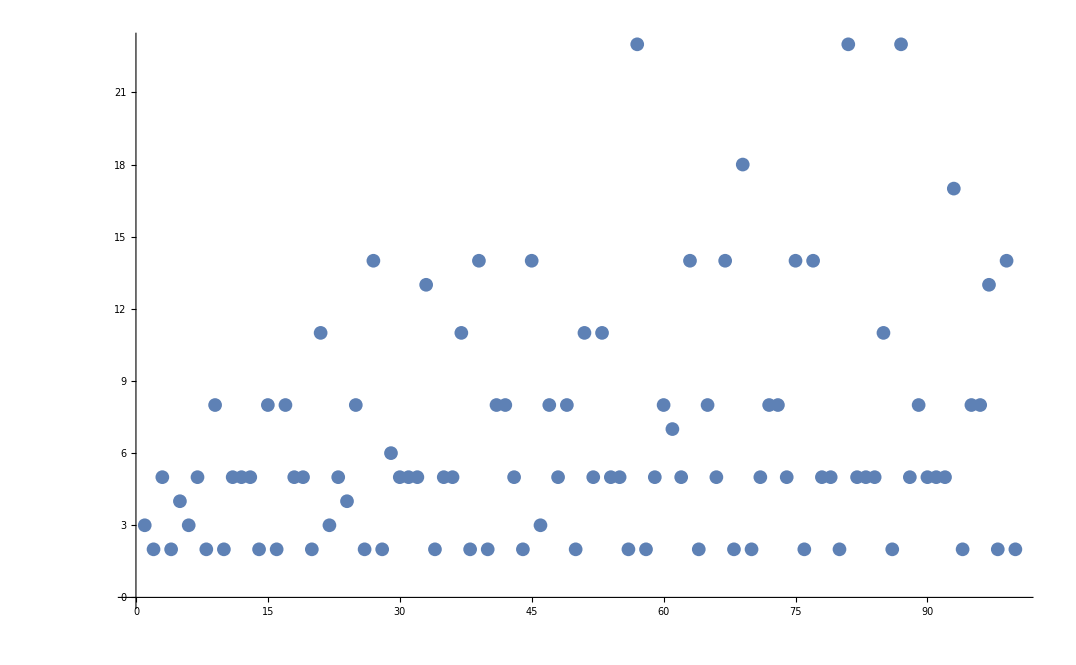

```mathematica
ListPlot[Take[nSolutions,100]]
```

```mathematica
Length[s[4]]
```

3

```mathematica
s[2]
s[4]
s[8]
```

{{x→4,y→4},{x→6,y→3}}

{{x→8,y→8},{x→12,y→6},{x→20,y→5}}

{{x→16,y→16},{x→24,y→12},{x→40,y→10},{x→72,y→9}}

```mathematica
s[2]
s[3]
s[6]
```

{{x→4,y→4},{x→6,y→3}}

{{x→6,y→6},{x→12,y→4}}

{{x→12,y→12},{x→15,y→10},{x→18,y→9},{x→24,y→8},{x→42,y→7}}

```mathematica
s[7]
```

{{x→14,y→14},{x→56,y→8}}

```mathematica
Length[Divisors[60]]
```

12

```mathematica
Length[s[60]]
```

23

```mathematica
n=∏_(i=1)^20 Prime[i]
Length[Divisors[n]]
Length[s[n]]
```

7858321551080267055879090

524288

```mathematica
Times @@ Table[Prime[n],{n,1,6}]
```

30030

```mathematica
Length[s[30030 2 3]]
```

1013

```mathematica
30030 6
```

180180

```mathematica
2 2 3 3 5 7 11 13
```

180180